## Дано

```mathematica
L1 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Методы вычислений\\Лабы\\lab3\\lab3\\Л_Рсетка.txt","Table"];
L2= Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Методы вычислений\\Лабы\\lab3\\lab3\\Л_Чсетка.txt","Table"];
```

```mathematica
C1 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Методы вычислений\\Лабы\\lab3\\lab3\\С_Рсетка.txt","Table"];
C2= Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Методы вычислений\\Лабы\\lab3\\lab3\\С_Чсетка.txt","Table"];
```

```mathematica
lp1 = ListLinePlot[L1,PlotStyle->Green,PlotRange->All];
```

```mathematica
lp2 = ListLinePlot[L2,PlotStyle->Blue,PlotRange->All];
```

```mathematica
cp1 = ListLinePlot[C1,PlotStyle->Green,PlotRange->All];
```

```mathematica
cp2 = ListLinePlot[C2,PlotStyle->Blue,PlotRange->All];
l1 = ListPlot[L1,PlotStyle->Green];
l2 = ListPlot[L2,PlotStyle->Blue];
c1 = ListPlot[C1,PlotStyle->Green];
c2 = ListPlot[C2,PlotStyle->Blue];
```

#### Графики

```mathematica
p0 = Plot[x,{x,-1,1},PlotStyle->{Red,Thick},PlotRange->All];
```

```mathematica
p1 = Plot[x^2,{x, -1,1},PlotStyle->{Red,Thick},PlotRange->All];
p2 = Plot[1/(1+x^2),{x, -1,1},PlotStyle->{Red,Thick},PlotRange->All];
p3 = Plot[1/ArcTan[1+10 x^2],{x, -3,3},PlotStyle->{Red,Thick},PlotRange->All];
p4 = Plot[(4 x^3+2 x^2-4x+2)^(√2)+ArcSin[1/(5+x-x^2)]-5,{x, -1,1},PlotStyle->{Red,Thick},PlotRange->All];
```

```mathematica
p5 = Plot[1/(1+25 x^2),{x, -1,1},PlotStyle->{Red,Thick},PlotRange->All];
```

```mathematica
p6 = Plot[1,{x,-1,1},PlotStyle->{Red,Thick},PlotRange->All];
```

```mathematica
p7 = Plot[Abs[x],{x,-1,1},PlotStyle->{Red,Thick},PlotRange->All];
```

## График

```mathematica
p=p7;
```

## Лагранж

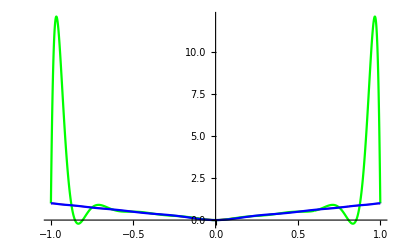

```mathematica
Show[p,lp1,lp2,PlotRange->All]
```

## Сплайн

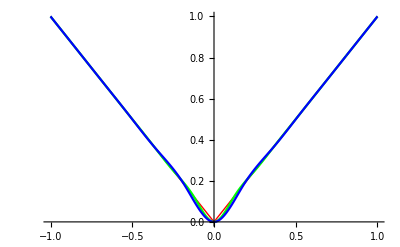

```mathematica
Show[p,cp1,cp2]
```

## Лагранж и сплайн

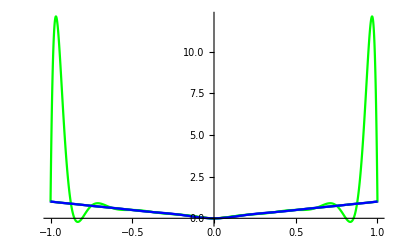

```mathematica
Show[p,lp1,lp2,cp1,cp2]
```